Parameters in sde: g=g/(ω^2 a), σ=(4π σ)/(m ω^2), η=(2ω σ a)/(3η R^2). Using ω=2π 10 Hz, a=1 mm, σ=0.073 N/m, η=1.8 10^-5 Pa s, R=2 mm, g=9.8 m/s^2. Considering the pressure distribution is a quadratic function of the radial displacement.

```mathematica
9.8/(4 π^2 10^2 0.001)
```

2.48237

```mathematica
(4π 0.073)/(1000 4/3 π(2 10^-3)^3 4 π^2 10^2)
```

6.93417

```mathematica
(2 2π 10 0.001)/(3 1.8 10^-5(2 10^-3)^2)
```

5.81776×10^8

```mathematica
sde=NDSolve[{x''[t]-y''[t]==4 π^2(-g+Cos[2π t]+σ y[t]),x'[t]+η x[t]^3/y[t]==0,x[0]==0.0001,y[0]==0.01,x'[0]==y'[0]==0}/.g->2.5/.σ->7./.η->5. 10^8,{x,y},{t,0,50}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{x→InterpolatingFunction[{{0., 50.}}, <>],y→InterpolatingFunction[{{0., 50.}}, <>]}}

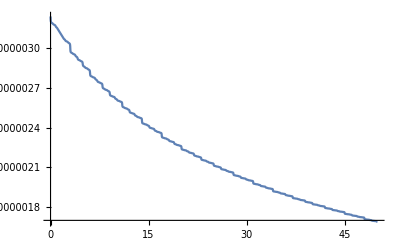

```mathematica
Plot[x[t]/.sde[[1]],{t,0,50}]
```

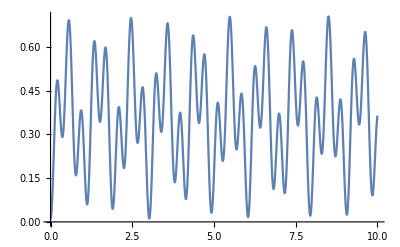

```mathematica
Plot[y[t]/.sde[[1]],{t,0,10}]
```